# Using PopulationGrowth to explore the Beverton and Holt model

```mathematica
<<EconMult`
```

## Options in PopulationGrowth

```mathematica
Options[PopulationGrowth]
```

{WeightLengthParameter→PGd,WeightLengthRelation→PGb,RichardsPellaTomlinsonParameter→PGmm,GrowthRate:>PGkk,SpawningBiomass:>PGSB,Recruits:>PGR,MortalityRate:>PGM,FishingMortalityRate:>PGF,MaxWeight→PGW8,MaxLength→PGL8,RecruitmentAge→PGtR,InitialAge→PGt0,CatchAge→PGtc,FirstCatchAge→PGtcs,OldestAge→PGt8,MaturationStartAge→PGtms,MaturationAge→PGtm,MaximumRecruitment→PGmR,MaximumRecruitmentBiomass→PGmRb,UseWeight→True,Fishing→True,DiscreteTime→False,BiomassSum→True,TimeStep→1,RecruitmentExponent→1,BiomassIncluded→Fishable,RecruitmentFunction→ConstantRecruitment,Maturation→Sharp,CatchSelection→Sharp,CatchStartPercentage→0.1,MaturationStartPercentage→0.1,CatchSelectionFunctionBend→2,PopulationModel→BevertonHoltModel,CurrentBiomass→PGX,GrowthModel→VerhulstSchaefer,RichardsPellaTomlinsonParameter→PGmm,MaximumSustainableYield→PGMSY,CatchabilityCoefficient→PGq,BiomassMaximum→PGK,IntrinsicGrowthRate→PGrr,UseMSY→True}

## Individual growth

```mathematica
Notation@vonBertalanffyLengthGrowth[t,UseWeight->False]
```

L'(t)==k (L_∞-L(t))

Solution:

```mathematica
Text@Row[{TraditionalForm[L[t]]," = ",Notation@LengthGrowth[t,UseWeight->False]}]
```

L(t) = L_∞ (1-ⅇ^(-k (t-t_0)))

when

```mathematica
Text@Row[{TraditionalForm[L[Subscript[t,0]]]," = 0"}]
```

L(t_0) = 0

Let

```mathematica
Text@Row[{TraditionalForm[W[t]]," = ",TraditionalForm[d*L[t]^b]}]
```

W(t) = d (L(t))^b

then

```mathematica
Text@Row[{TraditionalForm[W[t]]," = ",,Notation@IndividualWeight[t,UseWeight->False]}]
```

W(t) = d (L_∞ (1-ⅇ^(-k (t-t_0))))^b

or

```mathematica
Text@Row[{TraditionalForm[W[t]]," = ",,Notation@IndividualWeight[t,UseWeight->True]}]
```

W(t) = W_∞ (1-ⅇ^(-k (t-t_0)))^b

since

```mathematica
Text@Row[{TraditionalForm[Subscript[W,∞]]," = ",TraditionalForm[d*Subscript[L,∞]^b]}]
```

W_∞ = d L_∞^b

## Mortality

### Without fishing:

M is the natural mortality rate

```mathematica
Notation@BaranovMortality[t, Fishing->False]
```

N'(t)==-M N(t)

Solution:

```mathematica
Text@Row[{TraditionalForm["N"[t]]," = ",
DSolve[{
BaranovMortality[t, Fishing->False],
BaranovNumbers[PGtR]==Recruitment[PGSB]
},
BaranovNumbers[t],
t
][[1,1,2]]//SimplifyNotation}]
```

N(t) = R ⅇ^(M (t_R-t))

when recruitment takes place at age

```mathematica
TraditionalForm[Subscript[t,R]]
```

t_R

and R is a constant annual (or any other period) recruitment.

### With fishing:

F is the fishing mortality rate

```mathematica
Notation@BaranovMortality[t, Fishing->True]
```

N'(t)==-(F+M) N(t)

Solution:

```mathematica
Text@Row[{TraditionalForm["N"[t]]," = ",
DSolve[{
BaranovMortality[t, Fishing->True],
BaranovNumbers[PGtR]==Recruitment[PGSB]
},
BaranovNumbers[t],
t
][[1,1,2]]//SimplifyNotation}]
```

N(t) = R ⅇ^((F+M) (t_R-t))

## Cohort biomass

The biomass of one cohort at age t is

```mathematica
Text@Row[{TraditionalForm[x[t]]," = ",TraditionalForm["N"[t]*W[t]]," = ",Notation@CohortBiomass[t]}]
```

x(t) = N(t) W(t) = R W_∞ (1-ⅇ^(-k (t-t_0)))^b ⅇ^(-(F+M) (t-t_R))

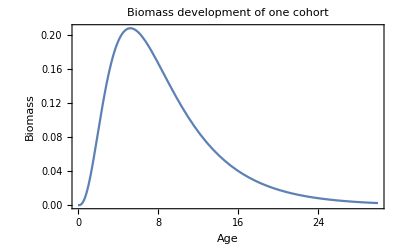

```mathematica
Plot[
CohortBiomass[
t,
InitialAge->0,
RecruitmentAge->0,
WeightLengthRelation->3,
GrowthRate->.35,
Recruits->1,
MaxWeight->1,
MortalityRate->.2,
Fishing->False
],
{t,0,30},
Frame->True,
FrameLabel->{"Age","Biomass"},
BaseStyle->{14,Italic},
PlotLabel->"Biomass development of one cohort"
]
```

```mathematica
IndividNumbers'[t]/IndividNumbers[t]//SimplifyNotation
```

-F-M

## The general Beverton and Holt model

```mathematica
PopulationGrowth[InitialAge->0]//Notation
```

(R W_∞ ⅇ^(-ⅈ π b+F t_c+M t_R) (ⅇ^(k t_∞)-(F+b k+M)/kb+1-ⅇ^(k t_c)-(F+b k+M)/kb+1))/k

```mathematica
PopulationGrowth[InitialAge->0,OldestAge->Infinity]//Notation
```

-(R W_∞ ⅇ^(-ⅈ π b+F t_c+M t_R) ⅇ^(k t_c)-(F+b k+M)/kb+1)/k

```mathematica
PopulationGrowth[WeightLengthRelation->3]//SimplifyNotation
```

R W_∞ ⅇ^(F t_c+M t_R) (-(3 ⅇ^(k t_0-t_c (F+k+M)))/(F+k+M)+(3 ⅇ^(2 k t_0-t_c (F+2 k+M)))/(F+2 k+M)-ⅇ^(3 k t_0-t_c (F+3 k+M))/(F+3 k+M)+ⅇ^(t_c (-(F+M)))/(F+M)+(3 ⅇ^(k t_0-t_∞ (F+k+M)))/(F+k+M)-(3 ⅇ^(2 k t_0-t_∞ (F+2 k+M)))/(F+2 k+M)+ⅇ^(3 k t_0-t_∞ (F+3 k+M))/(F+3 k+M)-ⅇ^(-(F+M) t_∞)/(F+M))

```mathematica
PopulationGrowth[WeightLengthRelation->3,OldestAge->Infinity]//Notation
```

-R W_∞ ⅇ^(M (t_R-t_c)) ((3 ⅇ^(k (t_0-t_c)))/(F+k+M)-(3 ⅇ^(2 k (t_0-t_c)))/(F+2 k+M)+ⅇ^(3 k (t_0-t_c))/(F+3 k+M)-1/(F+M))

```mathematica
PopulationGrowth[
InitialAge->0,
RecruitmentAge->0,
CatchAge->0,
OldestAge->Infinity,
WeightLengthRelation->3,
MortalityRate->GrowthRate
]//SimplifyNotation
```

(6 k^3 R W_∞)/((F+k) (F+2 k) (F+3 k) (F+4 k))

## Beverton and Holt model plots

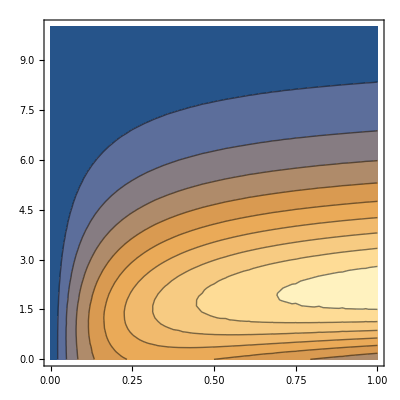

```mathematica
ContourPlot[F*PopulationGrowth[
FishingMortalityRate->F,
CatchAge->tc,
WeightLengthRelation->3,
GrowthRate->1/2,
Recruits->1,
MortalityRate->1/2,
MaxWeight->1,
RecruitmentAge->0,
InitialAge->0,
OldestAge->Infinity,
BiomassIncluded->Fishable,
Fishing->True
],
{F,0,1},
{tc,0,10},
MeshFunctions->{#3&}]
```

```mathematica
ContourPlot[TotalCatch[
FishingMortalityRate->F,
CatchAge->tc,
WeightLengthRelation->3,
GrowthRate->1/2,
Recruits->1,
MortalityRate->1/2,
MaxWeight->1,
RecruitmentAge->0,
InitialAge->0,
OldestAge->Infinity,
BiomassIncluded->Fishable,
Fishing->True
],
{F,0,1},
{tc,0,10},
MeshFunctions->{#3&}]
```

-Graphics-

```mathematica
Plot3D[TotalCatch[
FishingMortalityRate->F,
CatchAge->tc,
WeightLengthRelation->3,
GrowthRate->1/2,
Recruits->1,
MortalityRate->1/2,
MaxWeight->1,
RecruitmentAge->0,
InitialAge->0,
OldestAge->Infinity,
BiomassIncluded->Fishable,
Fishing->True
],
{F,0,1},
{tc,0,10},
MeshFunctions->{#3&}]
```

-Graphics3D-

## ..

```mathematica
Notation@PopulationGrowth[WeightLengthRelation->3,OldestAge->Infinity,InitialAge->0,BiomassIncluded->All,Fishing->True]
```

-R W_∞ ⅇ^(M (t_R-t_c)) (ⅇ^(-3 k t_c)/(F+3 k+M)-(3 ⅇ^(-2 k t_c))/(F+2 k+M)+(3 ⅇ^(-k t_c))/(F+k+M)-1/(F+M))-R W_∞ ⅇ^(M t_R) (-(3 (ⅇ^(t_c (-(k+M)))-1))/(k+M)+(3 (ⅇ^(t_c (-(2 k+M)))-1))/(2 k+M)-(ⅇ^(t_c (-(3 k+M)))-1)/(3 k+M)+(ⅇ^(-M t_c)-1)/M)

```mathematica
Notation@PopulationGrowth[
OldestAge->Infinity,InitialAge->0,WeightLengthRelation->3,BiomassIncluded->Fishable,Fishing->True]
```

-R W_∞ ⅇ^(M (t_R-t_c)) (ⅇ^(-3 k t_c)/(F+3 k+M)-(3 ⅇ^(-2 k t_c))/(F+2 k+M)+(3 ⅇ^(-k t_c))/(F+k+M)-1/(F+M))

```mathematica
Notation@PopulationGrowth[OldestAge->Infinity,InitialAge->0,WeightLengthRelation->3]
```

-R W_∞ ⅇ^(M (t_R-t_c)) (ⅇ^(-3 k t_c)/(F+3 k+M)-(3 ⅇ^(-2 k t_c))/(F+2 k+M)+(3 ⅇ^(-k t_c))/(F+k+M)-1/(F+M))

```mathematica
Notation@PopulationGrowth[InitialAge->0]
```

(R W_∞ ⅇ^(-ⅈ π b+F t_c+M t_R) (ⅇ^(k t_∞)-(F+b k+M)/kb+1-ⅇ^(k t_c)-(F+b k+M)/kb+1))/k

```mathematica
Notation@PopulationGrowth[InitialAge->0,CatchAge->0,OldestAge->Infinity]
```

(R W_∞ ⅇ^((F+M) t_R) 1(F+M)/kb+1)/k

```mathematica
Notation@PopulationBiomass[Infinity,InitialAge->0]
```

(R W_∞ ⅇ^((F+M) t_R) 1(F+M)/kb+1)/k

```mathematica
Notation@PopulationGrowth[InitialAge->0,CatchAge->0,OldestAge->10]
```

((-1)^-b R W_∞ ⅇ^((F+M) t_R) (-(F-k+M)/k ⅇ^(10 k)-(F+b k+M)/kb+1-b+1 -(F+b k+M)/k))/(k -(F-k+M)/k)

```mathematica
Notation@PopulationBiomass[10,InitialAge->0]
```

((-1)^-b R W_∞ ⅇ^((F+M) t_R) (-(F-k+M)/k ⅇ^(10 k)-(F+b k+M)/kb+1-b+1 -(F+b k+M)/k))/(k -(F-k+M)/k)

```mathematica
popbio[t_,opt___]:=PopulationGrowth[OldestAge->t,opt]
```

```mathematica
popbio[10,InitialAge->0,CatchAge->3]//Notation
```

(R W_∞ (ⅇ^(10 k)-(F+b k+M)/kb+1-ⅇ^(3 k)-(F+b k+M)/kb+1) ⅇ^(-ⅈ π b+3 F+M t_R))/k

```mathematica
Notation@PopulationGrowth[InitialAge->0,OldestAge->Infinity,BiomassIncluded->All]
```

((-1)^-b R W_∞ ⅇ^(M t_R) (-(M-k)/k ⅇ^(k t_c)-(b k+M)/kb+1-b+1 -(b k+M)/k))/(k -(M-k)/k)-(R W_∞ ⅇ^(-ⅈ π b+F t_c+M t_R) ⅇ^(k t_c)-(F+b k+M)/kb+1)/k

```mathematica
Notation@PopulationGrowth[InitialAge->0,OldestAge->Infinity,BiomassIncluded->Fishable,WeightLengthRelation->3]
```

-R W_∞ ⅇ^(M (t_R-t_c)) (ⅇ^(-3 k t_c)/(F+3 k+M)-(3 ⅇ^(-2 k t_c))/(F+2 k+M)+(3 ⅇ^(-k t_c))/(F+k+M)-1/(F+M))

```mathematica
Notation@PopulationGrowth[InitialAge->0,OldestAge->Infinity,BiomassIncluded->NotFishable]
```

((-1)^-b R W_∞ ⅇ^(M t_R) (-(M-k)/k ⅇ^(k t_c)-(b k+M)/kb+1-b+1 -(b k+M)/k))/(k -(M-k)/k)

## BiomassIncluded and Fishing

### Three values of BiomassIncluded

```mathematica
SimplifyNotation@PopulationGrowth[
WeightLengthRelation->3,
MortalityRate->GrowthRate,
InitialAge->0,
RecruitmentAge->0,
Fishing->True,
BiomassIncluded->#,OldestAge->t]&/@{NotFishable,Fishable,All}//TableForm
```

(R W_∞ ⅇ^(-4 k t_c) (ⅇ^(k t_c)-1)^4)/(4 k)
R W_∞ ⅇ^(F t_c) (-(3 ⅇ^(t_c (-(F+2 k))))/(F+2 k)+(3 ⅇ^(t_c (-(F+3 k))))/(F+3 k)-ⅇ^(t_c (-(F+4 k)))/(F+4 k)+ⅇ^(t_c (-(F+k)))/(F+k)+(3 ⅇ^(t (-(F+2 k))))/(F+2 k)-(3 ⅇ^(t (-(F+3 k))))/(F+3 k)+ⅇ^(t (-(F+4 k)))/(F+4 k)-ⅇ^(t (-(F+k)))/(F+k))
1/4 R W_∞ (4 ⅇ^(F t_c) (-(3 ⅇ^(t_c (-(F+2 k))))/(F+2 k)+(3 ⅇ^(t_c (-(F+3 k))))/(F+3 k)-ⅇ^(t_c (-(F+4 k)))/(F+4 k)+ⅇ^(t_c (-(F+k)))/(F+k)+(3 ⅇ^(t (-(F+2 k))))/(F+2 k)-(3 ⅇ^(t (-(F+3 k))))/(F+3 k)+ⅇ^(t (-(F+4 k)))/(F+4 k)-ⅇ^(t (-(F+k)))/(F+k))+(ⅇ^(-4 k t_c) (ⅇ^(k t_c)-1)^4)/k)

### PopulationGrowth with and without fishing

```mathematica
opt={
CatchAge->5,
WeightLengthRelation->3,
GrowthRate->.35,
Recruits->100,
MortalityRate->.2,
MaxWeight->10,
RecruitmentAge->1,
InitialAge->0};
```

```mathematica
Manipulate[Plot[
{PopulationGrowth[
OldestAge->t,
FishingMortalityRate->If[t<tc,0,F],
BiomassIncluded->All,
Fishing->True,
Sequence@@op[tc]
],
PopulationGrowth[
OldestAge->t,
BiomassIncluded->NotFishable,
Fishing->False,
Sequence@@op[tc]
]},
{t,0,15},GridLines->Automatic,PlotRange->{0,Automatic}],
{{tc,5},0,20,Appearance->"Labeled",ImageSize->Tiny},
{{F,.5},0,4,Appearance->"Labeled",ImageSize->Tiny},
Initialization->{
op[tc_]:={
CatchAge->tc,
WeightLengthRelation->2.9,
GrowthRate->.35,
Recruits->100,
MortalityRate->.2,
MaxWeight->10,
RecruitmentAge->1,
InitialAge->0}},
SaveDefinitions->True
]
```

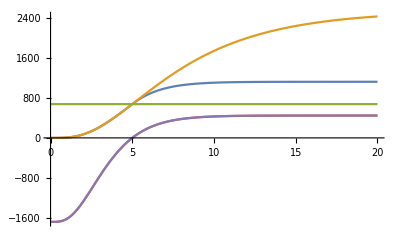

```mathematica
Plot[
{
PopulationGrowth[
OldestAge->t,
FishingMortalityRate->If[t<5,0,.5],
BiomassIncluded->All,
Fishing->True,
Sequence@@opt
],
PopulationGrowth[
OldestAge->t,
FishingMortalityRate->.5,
BiomassIncluded->NotFishable,
Fishing->False,
Sequence@@opt
],
PopulationGrowth[
OldestAge->t,
FishingMortalityRate->.5,
BiomassIncluded->NotFishable,
Fishing->True,
Sequence@@opt
],
PopulationGrowth[
OldestAge->t,
FishingMortalityRate->.5,
BiomassIncluded->Fishable,
Fishing->True,
Sequence@@opt
],
PopulationFractionBiomass[
OldestAge->t,
FishingMortalityRate->.5,
BiomassIncluded->Fishable,
Fishing->True,
Sequence@@opt
]
},
{t,0,20},PlotRange->All]
```

```mathematica
?PopulationBiomassOfMaxGrowth
```

PopulationBiomassOfMaxGrowth[opts] gives the population biomass corresponding to the maximum biomass growth when no fishing.

```mathematica
PopulationBiomassOfMaxGrowth[Sequence@@opt]
```

734.843

```mathematica
PopulationFractionBiomass[FishingMortalityRate->.5,OldestAge->10,Sequence@@opt]
```

428.297

```mathematica
PopulationGrowth[FishingMortalityRate->.5,OldestAge->10,Sequence@@opt]
```

428.297

```mathematica
PopulationBiomassOfMaxGrowth[WeightLengthRelation->3,InitialAge->0]//Notation
```

R (-((((3 k)/M+1)^(-M/k)-1)/M-(3 (((3 k)/M+1)^(-(k+M)/k)-1))/(k+M)+(3 (((3 k)/M+1)^(-(2 k+M)/k)-1))/(2 k+M)-(((3 k)/M+1)^(-(3 k+M)/k)-1)/(3 k+M))) W_∞ ⅇ^(M t_R)

### PopulationFractionBiomass is the fishable stock biomass

```mathematica
?PopulationFractionBiomass
```

PopulationFractionBiomass[opts] is a function used by BevertonHoltModel, giving the biomass of the population fraction between the ages of tc and t8.

```mathematica
PopulationFractionBiomass[InitialAge->0]//Notation
```

(R W_∞ ⅇ^(-ⅈ π b+F t_c+M t_R) (ⅇ^(k t_∞)-(F+b k+M)/kb+1-ⅇ^(k t_c)-(F+b k+M)/kb+1))/k

```mathematica
PopulationGrowth[InitialAge->0,BiomassIncluded->Fishable]//Notation
```

(R W_∞ ⅇ^(-ⅈ π b+F t_c+M t_R) (ⅇ^(k t_∞)-(F+b k+M)/kb+1-ⅇ^(k t_c)-(F+b k+M)/kb+1))/k

BiomassIncluded -> Fishable is the default option of PopulationGrowth

```mathematica
PopulationGrowth[InitialAge->0]//Notation
```

(R W_∞ ⅇ^(-ⅈ π b+F t_c+M t_R) (ⅇ^(k t_∞)-(F+b k+M)/kb+1-ⅇ^(k t_c)-(F+b k+M)/kb+1))/k

```mathematica
PopulationFractionBiomass[Sequence@@opt]//Notation
```

-1000 ⅇ^(5 F+0.2) (-ⅇ^(-(F+0.2) t_∞-1.05 t_∞)/(F+1.25)+(3 ⅇ^(-(F+0.2) t_∞-0.7 t_∞))/(F+0.9)-(3 ⅇ^(-(F+0.2) t_∞-0.35 t_∞))/(F+0.55)+ⅇ^(-(F+0.2) t_∞)/(F+0.2)+ⅇ^(-5 (F+0.2)-5.25)/(F+1.25)-(3 ⅇ^(-5 (F+0.2)-3.5))/(F+0.9)+(3 ⅇ^(-5 (F+0.2)-1.75))/(F+0.55)-ⅇ^(-5 (F+0.2))/(F+0.2))

```mathematica
PopulationGrowth[Sequence@@opt]//Notation
```

-1000 ⅇ^(5 F+0.2) (-ⅇ^(-(F+0.2) t_∞-1.05 t_∞)/(F+1.25)+(3 ⅇ^(-(F+0.2) t_∞-0.7 t_∞))/(F+0.9)-(3 ⅇ^(-(F+0.2) t_∞-0.35 t_∞))/(F+0.55)+ⅇ^(-(F+0.2) t_∞)/(F+0.2)+ⅇ^(-5 (F+0.2)-5.25)/(F+1.25)-(3 ⅇ^(-5 (F+0.2)-3.5))/(F+0.9)+(3 ⅇ^(-5 (F+0.2)-1.75))/(F+0.55)-ⅇ^(-5 (F+0.2))/(F+0.2))

Note: BiomassIncluded does not work in PopulationFractionBiomass

```mathematica
CohortBiomass[t,Sequence@@opt]
```

1000 ⅇ^(-(0.2+PGF) (-1+t)) (1-ⅇ^(-0.35 t))^3

### CohortBiomass assumes CatchAge = 0 at any fishing mortality rates.

```mathematica
PopulationFractionBiomass[FishingMortalityRate->.5,OldestAge->15,Sequence@@opt]
```

445.957

```mathematica
PopulationGrowth[FishingMortalityRate->.5,OldestAge->15,Sequence@@opt]
```

445.957

```mathematica
Integrate[CohortBiomass[t,FishingMortalityRate->.5,Sequence@@opt],{t,0,15}]
```

287.601

```mathematica
PopulationFractionBiomass[CatchAge->0,FishingMortalityRate->.5,OldestAge->15,Sequence@@opt]
```

287.601

```mathematica
PopulationGrowth[CatchAge->0,FishingMortalityRate->.5,OldestAge->15,Sequence@@opt]
```

287.601

```mathematica
Integrate[CohortBiomass[t,CatchAge->0,FishingMortalityRate->.5,Sequence@@opt],{t,0,15}]
```

287.601

### The relationship between fishing mortality, selection age and stock biomass

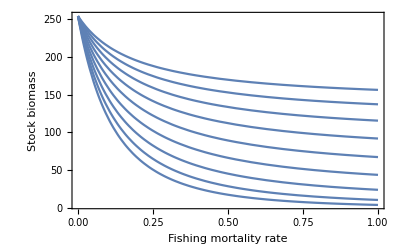

```mathematica
Show[
Table[Plot[
PopulationGrowth[
FishingMortalityRate->F,MaxWeight->1,OldestAge->Infinity,CatchAge->tc,BiomassIncluded->All,Sequence@@opt],
{F,0,1},PlotPoints->20],{tc,0,8}],PlotRange->All,Frame->True,FrameLabel->{"Fishing mortality rate","Stock biomass"}]
```

## TotalCatch

```mathematica
TotalCatch[]
```

PGF PGX

```mathematica
TotalCatch[]//Notation
```

F X

```mathematica
TotalCatch[InitialAge->0]//Notation
```

(F R W_∞ ⅇ^(-ⅈ π b+F t_c+M t_R) (ⅇ^(k t_∞)-(F+b k+M)/kb+1-ⅇ^(k t_c)-(F+b k+M)/kb+1))/k

```mathematica
TotalCatch[WeightLengthRelation->3,OldestAge->Infinity]//Notation
```

-F R W_∞ ⅇ^(M (t_R-t_c)) ((3 ⅇ^(k (t_0-t_c)))/(F+k+M)-(3 ⅇ^(2 k (t_0-t_c)))/(F+2 k+M)+ⅇ^(3 k (t_0-t_c))/(F+3 k+M)-1/(F+M))

```mathematica
opt={
CatchAge->5,
WeightLengthRelation->3,
GrowthRate->.35,
Recruits->100,
MortalityRate->.2,
MaxWeight->10,
RecruitmentAge->1,
InitialAge->0};
```

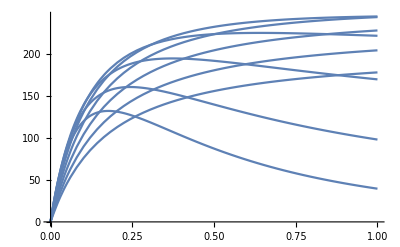

```mathematica
Show@Table[Plot[TotalCatch[CatchAge->tc,FishingMortalityRate->F,OldestAge->Infinity,Sequence@@opt],{F,0,1},PlotRange->All],{tc,0,8}]
```

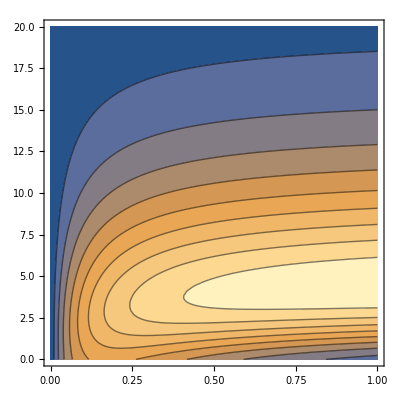

```mathematica
ContourPlot[TotalCatch[
FishingMortalityRate->F,
CatchAge->tc,
OldestAge->Infinity,
Sequence@@opt
],
{F,0,1},
{tc,0,20},
PlotPoints->35]
```

```mathematica
Plot3D[TotalCatch[
FishingMortalityRate->F,
CatchAge->tc,
OldestAge->Infinity,
Sequence@@opt
],
{F,0,1},
{tc,0,20},
PlotPoints->35,
MeshFunctions->{#3&}]
```

-Graphics3D-

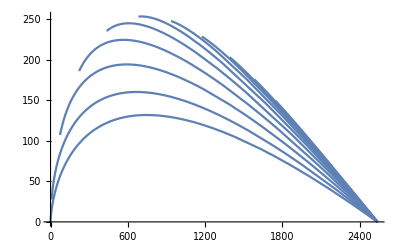

```mathematica
Show[
Table[ParametricPlot[
{PopulationGrowth[FishingMortalityRate->F,CatchAge->tc,OldestAge->Infinity,BiomassIncluded->All,Sequence@@opt],
TotalCatch[FishingMortalityRate->F,CatchAge->tc,OldestAge->Infinity,Sequence@@opt]},
{F,0,30},
AspectRatio->1/GoldenRatio,
PlotRange->{{0,EquilibriumBiomass[FishingMortalityRate->0,Sequence@@opt]},All}
],
{tc,0,10}]
]
```

```mathematica
opt={OldestAge->Infinity,InitialAge->0,WeightLengthRelation->3,MortalityRate->.2,GrowthRate->.35,MaxWeight->1,Recruits->1000,RecruitmentAge->0,FishingMortalityRate->0,BiomassIncluded->All};
```

```mathematica
yieldplot[tc0_]:=
Plot[Abs@YieldOfBiomass[x-(PopulationGrowth[BiomassIncluded->NotFishable,Sequence@@opt]/.{PGtc->tc0}),CatchAge->tc0,Sequence@@opt],{x,(PopulationGrowth[BiomassIncluded->NotFishable,Sequence@@opt]/.{PGtc->tc0}),(Apply[Plus,PopulationGrowth[Sequence@@opt]/.{PGtc->tc0}])}]
```

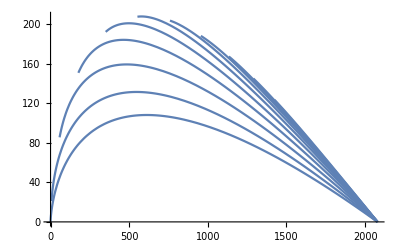

```mathematica
Show[Table[yieldplot[i],{i,0,10}], PlotRange->All]
```

## Derivatives of PopulationGrowth

```mathematica
opt={
CatchAge->5,
WeightLengthRelation->3,
GrowthRate->.35,
Recruits->100,
MortalityRate->.2,
MaxWeight->10,
RecruitmentAge->1,
InitialAge->0,
OldestAge->Infinity};
```

```mathematica
D[PopulationGrowth[WeightLengthRelation->3,InitialAge->0,OldestAge->Infinity],PGF]//Notation
```

-R W_∞ ⅇ^(M (t_R-t_c)) (-ⅇ^(-3 k t_c)/(F+3 k+M)^2+(3 ⅇ^(-2 k t_c))/(F+2 k+M)^2-(3 ⅇ^(-k t_c))/(F+k+M)^2+1/(F+M)^2)

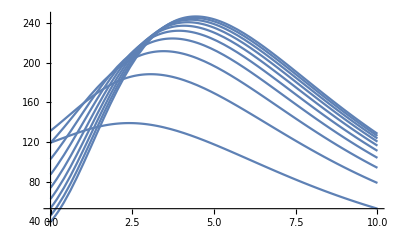

```mathematica
Show[Table[Plot[Evaluate[
D[PopulationGrowth[CatchAge->tc,FishingMortalityRate->F,BiomassIncluded->All,Sequence@@opt],tc]],{tc,0,10}],{F,.1,1,.1}],PlotRange->All]
```

```mathematica
Plot3D[Evaluate[D[PopulationGrowth[CatchAge->tc,FishingMortalityRate->F,BiomassIncluded->All,Sequence@@opt],tc]],{F,.001,1},{tc,0,10},PlotRange->All,PlotPoints->30,MeshFunctions->{#3&}]
```

-Graphics3D-

```mathematica
Plot3D[F PopulationGrowth[FishingMortalityRate->F,CatchAge->tc,Sequence@@opt],
{F,0,1},{tc,0,10},PlotPoints->30,MeshFunctions->{#3&}]
```

-Graphics3D-

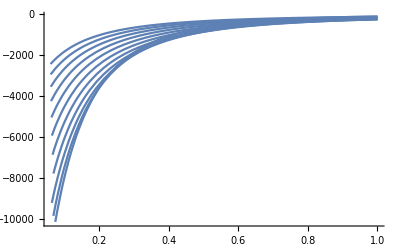

```mathematica
Show[Table[Plot[Evaluate[
D[PopulationGrowth[CatchAge->tc,FishingMortalityRate->F,BiomassIncluded->All,Sequence@@opt],F]],{F,.01,1}],{tc,0,10}],PlotRange->All]
```

```mathematica
Plot3D[Evaluate[D[PopulationGrowth[CatchAge->tc,FishingMortalityRate->F,BiomassIncluded->All,Sequence@@opt],F]],{tc,0,10},{F,.001,1},PlotRange->All,PlotPoints->30,MeshFunctions->{#3&}]
```

-Graphics3D-

## Discrete time

```mathematica
SimplifyNotation@PopulationBiomass[2,InitialAge->0,DiscreteTime->True,BiomassSum->False]
```

(0
R W_∞ (sinh(k)-cosh(k)+1)^b ⅇ^((F+M) (t_R-1))
R (1-ⅇ^(-2 k))^b W_∞ ⅇ^((F+M) (t_R-2)))

```mathematica
Notation@PopulationGrowth[OldestAge->5,InitialAge->0,WeightLengthRelation->3,MortalityRate->GrowthRate,Fishing->True,DiscreteTime->True,BiomassIncluded->All,BiomassSum->All,CatchAge->3]
```

(0
(1-ⅇ^-k)^3 R W_∞ ⅇ^(-k (1-t_R))
(1-ⅇ^(-2 k))^3 R W_∞ ⅇ^(-k (2-t_R))
(1-ⅇ^(-3 k))^3 R W_∞ ⅇ^(-(F+k) (3-t_R))
(1-ⅇ^(-4 k))^3 R W_∞ ⅇ^(-(F+k) (4-t_R))
(1-ⅇ^(-5 k))^3 R W_∞ ⅇ^(-(F+k) (5-t_R)))

```mathematica
Notation@PopulationBiomass[10,InitialAge->0,WeightLengthRelation->3,MortalityRate->GrowthRate,Fishing->True,
BiomassIncluded->All,DiscreteTime->True,BiomassSum->False,CatchAge->3]
```

(0
(1-ⅇ^-k)^3 R W_∞ ⅇ^(-(F+k) (1-t_R))
(1-ⅇ^(-2 k))^3 R W_∞ ⅇ^(-(F+k) (2-t_R))
(1-ⅇ^(-3 k))^3 R W_∞ ⅇ^(-(F+k) (3-t_R))
(1-ⅇ^(-4 k))^3 R W_∞ ⅇ^(-(F+k) (4-t_R))
(1-ⅇ^(-5 k))^3 R W_∞ ⅇ^(-(F+k) (5-t_R))
(1-ⅇ^(-6 k))^3 R W_∞ ⅇ^(-(F+k) (6-t_R))
(1-ⅇ^(-7 k))^3 R W_∞ ⅇ^(-(F+k) (7-t_R))
(1-ⅇ^(-8 k))^3 R W_∞ ⅇ^(-(F+k) (8-t_R))
(1-ⅇ^(-9 k))^3 R W_∞ ⅇ^(-(F+k) (9-t_R))
(1-ⅇ^(-10 k))^3 R W_∞ ⅇ^(-(F+k) (10-t_R)))

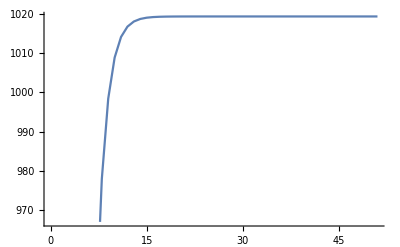

```mathematica
NestList[PopulationGrowth[
FishingMortalityRate->0.1,
CatchAge->0,
WeightLengthRelation->3,
GrowthRate->.4,
MortalityRate->.2,
MaxWeight->1,
RecruitmentAge->3,
InitialAge->0,
OldestAge->Infinity,
BiomassIncluded->All,
Fishing->True,
RecruitmentFunction->BevertonHoltRecruitment,
MaximumRecruitmentBiomass->2000,MaximumRecruitment->1000,
SpawningBiomass->#
]&,
150,50]//ListLinePlot
```

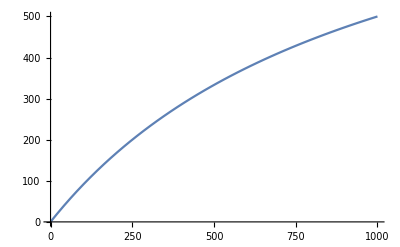

```mathematica
Plot[Recruitment[S,RecruitmentFunction->BevertonHoltRecruitment,MaximumRecruitmentBiomass->2000,MaximumRecruitment->1000],{S,0,1000}]
```

```mathematica
opt={CatchAge->0,InitialAge->0,OldestAge->Infinity,WeightLengthRelation->3,MortalityRate->.2,GrowthRate->.35,MaxWeight->1,Recruits->1000,RecruitmentAge->0,FishingMortalityRate->0};
```

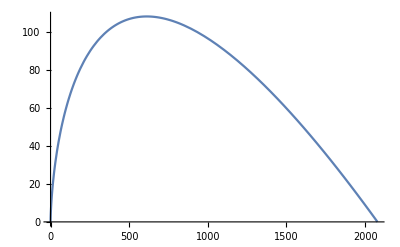

```mathematica
Plot[YieldOfBiomass[x,Sequence@@opt],{x,0,PopulationGrowth[Sequence@@opt]}]
```

```mathematica
PopulationGrowth[Sequence@@opt]
```

2078.79

```mathematica
EquilibriumBiomass[Sequence@@opt]
```

2078.79

## Identities

### PopulationBiomass[Infinity,InitialAge→0] is identical to PopulationGrowth[InitialAge→0,OldestAge→Infinity,CatchAge→0]

```mathematica
PopulationBiomass[Infinity,InitialAge->0]//Notation
```

(R W_∞ ⅇ^((F+M) t_R) 1(F+M)/kb+1)/k

```mathematica
PopulationGrowth[InitialAge->0,OldestAge->Infinity,CatchAge->0]//Notation
```

(R W_∞ ⅇ^((F+M) t_R) 1(F+M)/kb+1)/k

```mathematica
PopulationBiomass[Infinity,InitialAge->0]==PopulationGrowth[InitialAge->0,OldestAge->Infinity,CatchAge->0]
```

True

### EquilibriumBiomass[ ] is identical to PopulationGrowth[CatchAge → 0, OldestAge → Infinity]

```mathematica
Notation@EquilibriumBiomass[]
```

(R W_∞ ⅇ^(-(F+M) (t_0-t_R)) ⅇ^(k t_0)(F+M)/kb+1)/k

```mathematica
Notation@PopulationGrowth[CatchAge->0,OldestAge->Infinity]
```

(R W_∞ ⅇ^(-(F+M) (t_0-t_R)) ⅇ^(k t_0)(F+M)/kb+1)/k

```mathematica
EquilibriumBiomass[]===PopulationGrowth[CatchAge->0,OldestAge->Infinity]
```

True

```mathematica
PopulationGrowth[OldestAge->Infinity]===BevertonHoltModel[OldestAge->Infinity]
```

True

## test

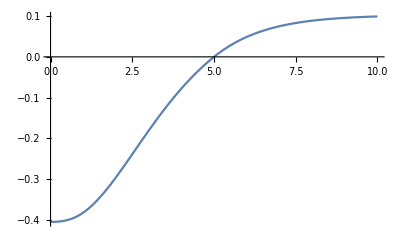
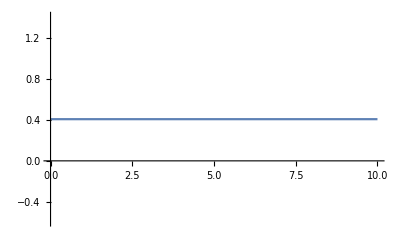
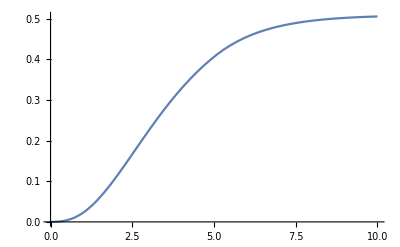

```mathematica
Plot[PopulationGrowth[
FishingMortalityRate->If[t<5,0,.2],
CatchAge->5,
WeightLengthRelation->3,
GrowthRate->1/2,
Recruits->1,
MortalityRate->1/2,
MaxWeight->1,
RecruitmentAge->0,
InitialAge->-.2,
OldestAge->t,
Fishing->True,
BiomassIncluded->#
],{t,0,10},PlotRange->All]&/@{Fishable,NotFishable,All}
```

```mathematica
NoFishing=PopulationGrowth[
FishingMortalityRate->.2,
CatchAge->5,
WeightLengthRelation->3,
GrowthRate->1/2,
Recruits->1,
MortalityRate->1/2,
MaxWeight->1,
RecruitmentAge->0,
InitialAge->-.2,
Fishing->True,
BiomassIncluded->NotFishable
]
```

0.405772

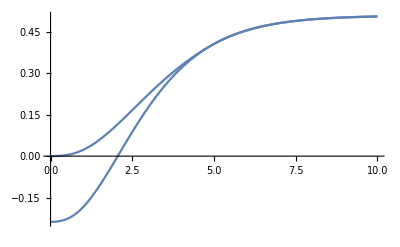

```mathematica
Show[
Plot[PopulationGrowth[
FishingMortalityRate->.2,
CatchAge->5,
WeightLengthRelation->3,
GrowthRate->1/2,
Recruits->1,
MortalityRate->1/2,
MaxWeight->1,
RecruitmentAge->0,
InitialAge->-.2,
OldestAge->t,
Fishing->True,
BiomassIncluded->Fishable
]+NoFishing,{t,0,10},PlotRange->All],
Plot[PopulationGrowth[
FishingMortalityRate->If[t<5,0,.2],
CatchAge->5,
WeightLengthRelation->3,
GrowthRate->1/2,
Recruits->1,
MortalityRate->1/2,
MaxWeight->1,
RecruitmentAge->0,
InitialAge->-.2,
OldestAge->t,
Fishing->True,
BiomassIncluded->All
],{t,0,10},PlotRange->All]
]
```

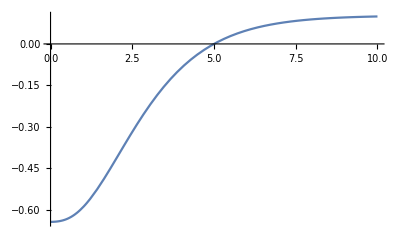
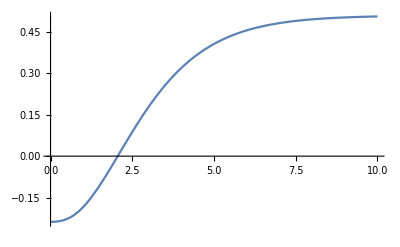
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Plot[PopulationGrowth[
FishingMortalityRate->.2,
CatchAge->5,
WeightLengthRelation->3,
GrowthRate->1/2,
Recruits->1,
MortalityRate->1/2,
MaxWeight->1,
RecruitmentAge->0,
InitialAge->-.2,
OldestAge->t,
Fishing->True,
BiomassIncluded->#
],{t,0,10},PlotRange->All]&/@{Fishable,NotFishable,All}
```

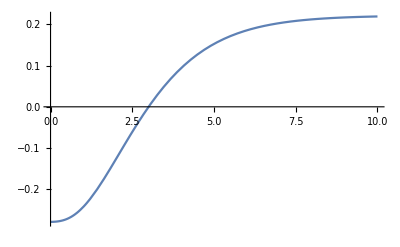
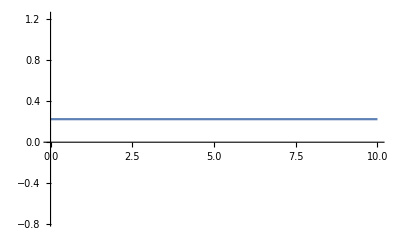
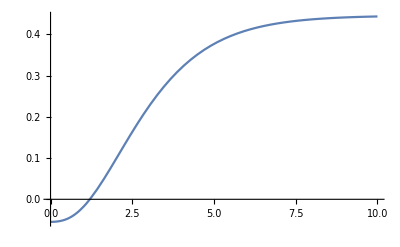

```mathematica
Plot[BevertonHoltModel[
FishingMortalityRate->.2,
CatchAge->3,
WeightLengthRelation->3,
GrowthRate->1/2,
Recruits->1,
MortalityRate->1/2,
MaxWeight->1,
RecruitmentAge->0,
InitialAge->-.2,
OldestAge->t,
Fishing->True,
BiomassIncluded->#
],{t,0,10},PlotRange->All]&/@{Fishable,NotFishable,All}
```

```mathematica
Plot[BevertonHoltModel[
FishingMortalityRate->.2,
CatchAge->3,
WeightLengthRelation->3,
GrowthRate->1/2,
Recruits->1,
MortalityRate->1/2,
MaxWeight->1,
RecruitmentAge->0,
InitialAge->-.2,
OldestAge->t,
Fishing->True,
BiomassIncluded->#,
SelectionFunction->Logistic,
FirstCatchAge->0
],{t,0,10},PlotRange->All]&/@{Fishable,NotFishable,All}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
??PopulationBiomass
```

PopulationBiomass[t, opts] gives biomass sum of population between RecruitmentAge and age t.

PopulationBiomass[IndividAge_,EconMult`PopulationGrowth`Private`opts___]:=Module[{EconMult`PopulationGrowth`Private`d,EconMult`PopulationGrowth`Private`b,EconMult`PopulationGrowth`Private`m,EconMult`PopulationGrowth`Private`k,EconMult`PopulationGrowth`Private`S,EconMult`PopulationGrowth`Private`R,EconMult`PopulationGrowth`Private`M,EconMult`PopulationGrowth`Private`F,EconMult`PopulationGrowth`Private`W8,EconMult`PopulationGrowth`Private`L8,EconMult`PopulationGrowth`Private`tR,EconMult`PopulationGrowth`Private`t0,EconMult`PopulationGrowth`Private`tc,EconMult`PopulationGrowth`Private`t8,EconMult`PopulationGrowth`Private`uw,EconMult`PopulationGrowth`Private`f,EconMult`PopulationGrowth`Private`dt,EconMult`PopulationGrowth`Private`bs,EconMult`PopulationGrowth`Private`ts,EconMult`PopulationGrowth`Private`bi,EconMult`PopulationGrowth`Private`mr,EconMult`PopulationGrowth`Private`mrb,EconMult`PopulationGrowth`Private`re,EconMult`PopulationGrowth`Private`rf,EconMult`PopulationGrowth`Private`ma,EconMult`PopulationGrowth`Private`cs,EconMult`PopulationGrowth`Private`tms,EconMult`PopulationGrowth`Private`tm,EconMult`PopulationGrowth`Private`sfb,EconMult`PopulationGrowth`Private`tcs,EconMult`PopulationGrowth`Private`csp,EconMult`PopulationGrowth`Private`msp,EconMult`PopulationGrowth`Private`t,EconMult`PopulationGrowth`Private`cfs},{EconMult`PopulationGrowth`Private`d,EconMult`PopulationGrowth`Private`b,EconMult`PopulationGrowth`Private`m,EconMult`PopulationGrowth`Private`k,EconMult`PopulationGrowth`Private`S,EconMult`PopulationGrowth`Private`R,EconMult`PopulationGrowth`Private`M,EconMult`PopulationGrowth`Private`F,EconMult`PopulationGrowth`Private`W8,EconMult`PopulationGrowth`Private`L8,EconMult`PopulationGrowth`Private`tR,EconMult`PopulationGrowth`Private`t0,EconMult`PopulationGrowth`Private`tc,EconMult`PopulationGrowth`Private`t8,EconMult`PopulationGrowth`Private`uw,EconMult`PopulationGrowth`Private`f,EconMult`PopulationGrowth`Private`dt,EconMult`PopulationGrowth`Private`bs,EconMult`PopulationGrowth`Private`ts,EconMult`PopulationGrowth`Private`bi,EconMult`PopulationGrowth`Private`mr,EconMult`PopulationGrowth`Private`mrb,EconMult`PopulationGrowth`Private`re,EconMult`PopulationGrowth`Private`rf,EconMult`PopulationGrowth`Private`ma,EconMult`PopulationGrowth`Private`cs,EconMult`PopulationGrowth`Private`tms,EconMult`PopulationGrowth`Private`tm,EconMult`PopulationGrowth`Private`sfb,EconMult`PopulationGrowth`Private`tcs,EconMult`PopulationGrowth`Private`csp,EconMult`PopulationGrowth`Private`msp}=EconMult`PopulationGrowth`Private`optionslist/.{EconMult`PopulationGrowth`Private`opts}/.Options[PopulationGrowth];If[EconMult`PopulationGrowth`Private`rf===BevertonHoltRecruitment||EconMult`PopulationGrowth`Private`rf===RickerRecruitment,EconMult`PopulationGrowth`Private`R=Recruitment[EconMult`PopulationGrowth`Private`S,EconMult`PopulationGrowth`Private`opts]];If[!EconMult`PopulationGrowth`Private`uw,EconMult`PopulationGrowth`Private`W8=EconMult`PopulationGrowth`Private`d (EconMult`PopulationGrowth`Private`L8)^(EconMult`PopulationGrowth`Private`b)];If[!EconMult`PopulationGrowth`Private`f,EconMult`PopulationGrowth`Private`F=0];If[EconMult`PopulationGrowth`Private`dt,EconMult`PopulationGrowth`Private`cfs=Table[CohortBiomass[EconMult`PopulationGrowth`Private`t,EconMult`PopulationGrowth`Private`opts],{EconMult`PopulationGrowth`Private`t,0,IndividAge,EconMult`PopulationGrowth`Private`ts}];If[EconMult`PopulationGrowth`Private`bs,EconMult`PopulationGrowth`Private`ts Plus@@EconMult`PopulationGrowth`Private`cfs,EconMult`PopulationGrowth`Private`cfs,EconMult`PopulationGrowth`Private`cfs],If[IndividAge===∞,If[EconMult`PopulationGrowth`Private`b===3,-(ⅇ^(EconMult`PopulationGrowth`Private`M EconMult`PopulationGrowth`Private`tR) (-1/(EconMult`PopulationGrowth`Private`F+EconMult`PopulationGrowth`Private`M)+(3 ⅇ^(EconMult`PopulationGrowth`Private`k EconMult`PopulationGrowth`Private`t0))/(EconMult`PopulationGrowth`Private`F+EconMult`PopulationGrowth`Private`k+EconMult`PopulationGrowth`Private`M)-(3 ⅇ^(2 EconMult`PopulationGrowth`Private`k EconMult`PopulationGrowth`Private`t0))/(EconMult`PopulationGrowth`Private`F+2 EconMult`PopulationGrowth`Private`k+EconMult`PopulationGrowth`Private`M)+ⅇ^(3 EconMult`PopulationGrowth`Private`k EconMult`PopulationGrowth`Private`t0)/(EconMult`PopulationGrowth`Private`F+3 EconMult`PopulationGrowth`Private`k+EconMult`PopulationGrowth`Private`M)) EconMult`PopulationGrowth`Private`R EconMult`PopulationGrowth`Private`W8),(EconMult`PopulationGrowth`Private`R EconMult`PopulationGrowth`Private`W8 Beta[ⅇ^(EconMult`PopulationGrowth`Private`k EconMult`PopulationGrowth`Private`t0),(EconMult`PopulationGrowth`Private`F+EconMult`PopulationGrowth`Private`M)/(EconMult`PopulationGrowth`Private`k),1+EconMult`PopulationGrowth`Private`b])/(ⅇ^((EconMult`PopulationGrowth`Private`F+EconMult`PopulationGrowth`Private`M) (EconMult`PopulationGrowth`Private`t0-EconMult`PopulationGrowth`Private`tR)) EconMult`PopulationGrowth`Private`k)],If[EconMult`PopulationGrowth`Private`b===3,-(ⅇ^((EconMult`PopulationGrowth`Private`F+EconMult`PopulationGrowth`Private`M) EconMult`PopulationGrowth`Private`tR) ((-1+ⅇ^(-((EconMult`PopulationGrowth`Private`F+EconMult`PopulationGrowth`Private`M) IndividAge)))/(EconMult`PopulationGrowth`Private`F+EconMult`PopulationGrowth`Private`M)-(3 ⅇ^(EconMult`PopulationGrowth`Private`k EconMult`PopulationGrowth`Private`t0) (-1+ⅇ^(-((EconMult`PopulationGrowth`Private`F+EconMult`PopulationGrowth`Private`k+EconMult`PopulationGrowth`Private`M) IndividAge))))/(EconMult`PopulationGrowth`Private`F+EconMult`PopulationGrowth`Private`k+EconMult`PopulationGrowth`Private`M)+(3 ⅇ^(2 EconMult`PopulationGrowth`Private`k EconMult`PopulationGrowth`Private`t0) (-1+ⅇ^(-((EconMult`PopulationGrowth`Private`F+2 EconMult`PopulationGrowth`Private`k+EconMult`PopulationGrowth`Private`M) IndividAge))))/(EconMult`PopulationGrowth`Private`F+2 EconMult`PopulationGrowth`Private`k+EconMult`PopulationGrowth`Private`M)-(ⅇ^(3 EconMult`PopulationGrowth`Private`k EconMult`PopulationGrowth`Private`t0) (-1+ⅇ^(-((EconMult`PopulationGrowth`Private`F+3 EconMult`PopulationGrowth`Private`k+EconMult`PopulationGrowth`Private`M) IndividAge))))/(EconMult`PopulationGrowth`Private`F+3 EconMult`PopulationGrowth`Private`k+EconMult`PopulationGrowth`Private`M)) EconMult`PopulationGrowth`Private`R EconMult`PopulationGrowth`Private`W8),If[EconMult`PopulationGrowth`Private`t0===0,If[EconMult`PopulationGrowth`Private`M===EconMult`PopulationGrowth`Private`k,(ⅇ^(EconMult`PopulationGrowth`Private`k (EconMult`PopulationGrowth`Private`tR-(1+EconMult`PopulationGrowth`Private`b) IndividAge)) (-1+ⅇ^(EconMult`PopulationGrowth`Private`k IndividAge))^(1+EconMult`PopulationGrowth`Private`b) EconMult`PopulationGrowth`Private`R EconMult`PopulationGrowth`Private`W8)/((1+EconMult`PopulationGrowth`Private`b) EconMult`PopulationGrowth`Private`k),(ⅇ^((EconMult`PopulationGrowth`Private`F+EconMult`PopulationGrowth`Private`M) EconMult`PopulationGrowth`Private`tR) EconMult`PopulationGrowth`Private`R EconMult`PopulationGrowth`Private`W8 (Beta[ⅇ^(EconMult`PopulationGrowth`Private`k IndividAge),-(EconMult`PopulationGrowth`Private`F+EconMult`PopulationGrowth`Private`b EconMult`PopulationGrowth`Private`k+EconMult`PopulationGrowth`Private`M)/(EconMult`PopulationGrowth`Private`k),1+EconMult`PopulationGrowth`Private`b] Gamma[-(EconMult`PopulationGrowth`Private`F-EconMult`PopulationGrowth`Private`k+EconMult`PopulationGrowth`Private`M)/(EconMult`PopulationGrowth`Private`k)]-Gamma[1+EconMult`PopulationGrowth`Private`b] Gamma[-(EconMult`PopulationGrowth`Private`F+EconMult`PopulationGrowth`Private`b EconMult`PopulationGrowth`Private`k+EconMult`PopulationGrowth`Private`M)/(EconMult`PopulationGrowth`Private`k)]))/((-1)^(EconMult`PopulationGrowth`Private`b) EconMult`PopulationGrowth`Private`k Gamma[-(EconMult`PopulationGrowth`Private`F-EconMult`PopulationGrowth`Private`k+EconMult`PopulationGrowth`Private`M)/(EconMult`PopulationGrowth`Private`k)])],If[EconMult`PopulationGrowth`Private`k===EconMult`PopulationGrowth`Private`M+EconMult`PopulationGrowth`Private`F,((-(ⅇ^(EconMult`PopulationGrowth`Private`k (EconMult`PopulationGrowth`Private`t0+IndividAge+EconMult`PopulationGrowth`Private`b IndividAge)) (1-ⅇ^(EconMult`PopulationGrowth`Private`k EconMult`PopulationGrowth`Private`t0))^(1+EconMult`PopulationGrowth`Private`b))+ⅇ^(EconMult`PopulationGrowth`Private`k EconMult`PopulationGrowth`Private`t0) (-ⅇ^(EconMult`PopulationGrowth`Private`k EconMult`PopulationGrowth`Private`t0)+ⅇ^(EconMult`PopulationGrowth`Private`k IndividAge))^(1+EconMult`PopulationGrowth`Private`b)) EconMult`PopulationGrowth`Private`R EconMult`PopulationGrowth`Private`W8)/(ⅇ^(EconMult`PopulationGrowth`Private`k (2 EconMult`PopulationGrowth`Private`t0-EconMult`PopulationGrowth`Private`tR+IndividAge+EconMult`PopulationGrowth`Private`b IndividAge)) (1+EconMult`PopulationGrowth`Private`b) EconMult`PopulationGrowth`Private`k),If[NumberQ[EconMult`PopulationGrowth`Private`b]&&NumberQ[EconMult`PopulationGrowth`Private`k]&&NumberQ[EconMult`PopulationGrowth`Private`R]&&NumberQ[EconMult`PopulationGrowth`Private`M]&&NumberQ[EconMult`PopulationGrowth`Private`F]&&NumberQ[EconMult`PopulationGrowth`Private`tR]&&NumberQ[EconMult`PopulationGrowth`Private`t0]&&(NumberQ[EconMult`PopulationGrowth`Private`W8]||(NumberQ[EconMult`PopulationGrowth`Private`L8]&&NumberQ[EconMult`PopulationGrowth`Private`d])),NIntegrate[CohortBiomass[EconMult`PopulationGrowth`Private`t,EconMult`PopulationGrowth`Private`opts],{EconMult`PopulationGrowth`Private`t,0,IndividAge}],PGX]]]]]]]